#### import data

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/Band_life_broadened/TOTAL"];
filesLINE={"c.lw.10","c.lw.300","c.lw.1000","c.lw.3800"};
(*Exclude the DOS with zero smearing*)
lineWidths=Table[ReadList[filesLINE[[i]],{Number,Number,Number,Number,Number,Number,Number}],{i,1,filesLINE//Length}];
bands=ReadList["clong.bands",{Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
{
```

```mathematica
b=Table[DeleteDuplicates@Transpose[{Transpose[bands][[1]],Transpose[bands][[i+1]]}],{i,1,Length[Transpose[bands]]-1}];
```

```mathematica
lw10=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[1]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[1]]]]-1}];
lw300=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[2]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[2]]]]-1}];
lw1000=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[3]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[3]]]]-1}];
lw3800=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[4]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[4]]]]-1}];
```

```mathematica
interb=Table[Interpolation[b[[i]]],{i,1,Length[b]}];
interlw10=Table[Interpolation[lw10[[i]]],{i,1,Length[lw10]}];
interlw300=Table[Interpolation[lw300[[i]]],{i,1,Length[lw300]}];
interlw1000=Table[Interpolation[lw1000[[i]]],{i,1,Length[lw1000]}];
interlw3800=Table[Interpolation[lw3800[[i]]],{i,1,Length[lw3800]}];
```

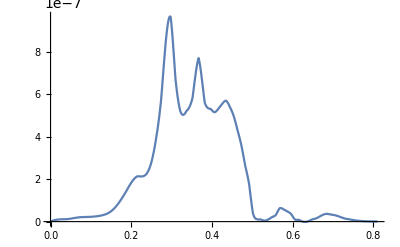

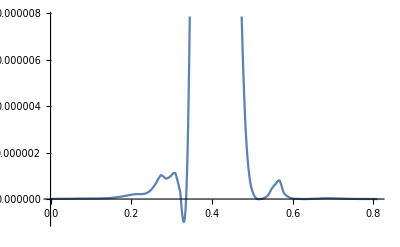

```mathematica
Plot[interlw10[[1]][x],{x,0,0.81}]
Plot[interlw10[[2]][x],{x,0,0.81}]
```

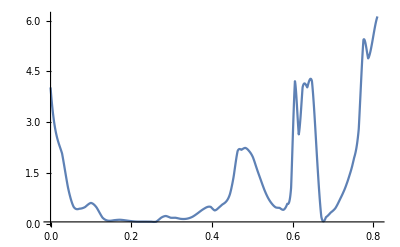

```mathematica
Plot[interlw3800[[6]][x],{x,0,0.81},PlotRange->All]
```

```mathematica
Norm[-1]
```

1

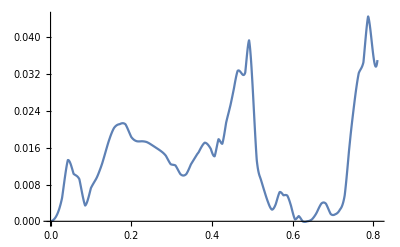

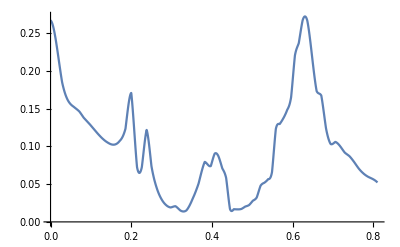

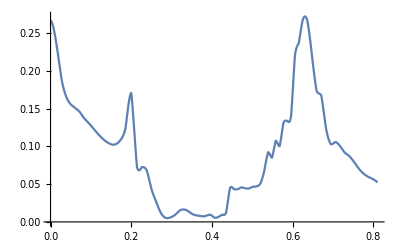

```mathematica
Plot[interlw300[[3]][x],{x,0,0.81}]
Plot[interlw300[[4]][x],{x,0,0.81}]

Plot[interlw300[[5]][x],{x,0,0.81}]
```

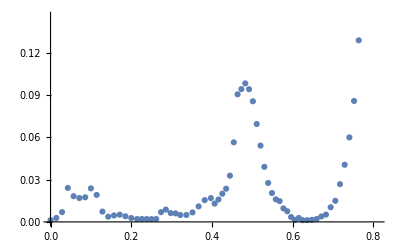

```mathematica
ListPlot@interlw10[[6]]
```

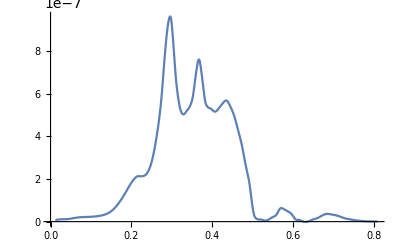

```mathematica
ListLinePlot[Table[MovingAverage[Table[{x,(interlw10[[i]][x])},{x,0.01,0.81,0.001}],5],{i,1,1}],PlotRange->All]
```

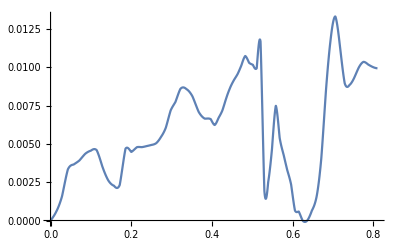

```mathematica
Plot[interlw300[[1]][x],{x,0,0.81}]
```

```mathematica
FindMinimum[interlw300[[1]][x],x]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.0000907661,{x→0.630181}}

```mathematica
interlw300[[1]][x]/.FindMaximum[interlw300[[1]][x],x,{0.01,0.8}][[2]]
```

FindMaximum::ivar: 0.01 is not a valid variable.

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

InterpolatingFunction[{{0., 0.81005}}, <>][x]/.x

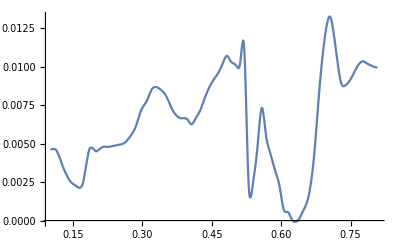

```mathematica
ListLinePlot[Table[MovingAverage[Table[{x,(interlw300[[i]][x])},{x,0.1,0.81,0.001}],5],{i,1,1}],PlotRange->All]
```

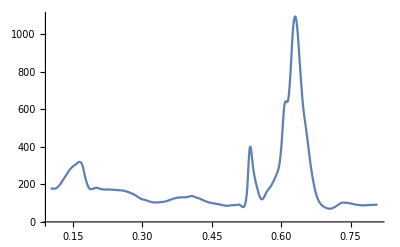

```mathematica
ListLinePlot[Table[MovingAverage[Table[{x,1/(interlw300[[i]][x]+0.001)},{x,0.1,0.81,0.001}],5],{i,1,1}],PlotRange->All]
```

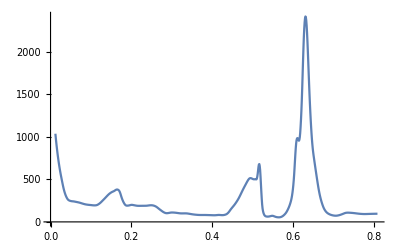

```mathematica
ListLinePlot[Table[MovingAverage[Table[{x,1/(interlw300[[i]][x]+0.0005)},{x,0.01,0.81,0.001}],5],{i,2,2}],PlotRange->All]
```

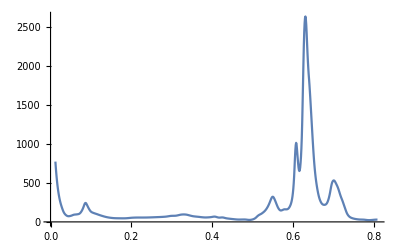

```mathematica
ListLinePlot[Table[MovingAverage[Table[{x,1/(interlw300[[i]][x]+0.0005)},{x,0.01,0.81,0.001}],5],{i,3,3}],PlotRange->All]
```

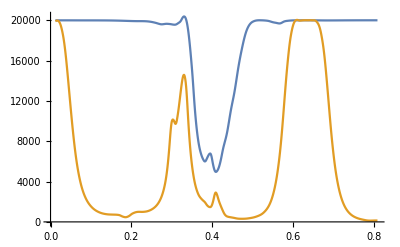

```mathematica
ListLinePlot[Table[MovingAverage[Table[{x,1/(interlw10[[i]][x]+0.00005)},{x,0.01,0.81,0.001}],5],{i,2,3}],PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0000165471} lies outside the range of data in the interpolating function. Extrapolation will be used.

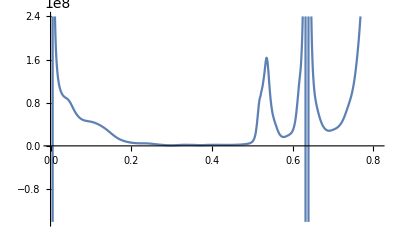

```mathematica
Plot[1/Interpolation[MovingMap[Mean,Table[{x,interlw10[[1]][x]},{x,0,0.814,0.005}],{0.01}]][x],{x,0,0.81}]
```

```mathematica
DensityPlot[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"z-value"]]
```

```mathematica
With[{height=40,width=5,baseWidth=0.01},Table[(baseWidth+height)*PDF[CauchyDistribution[1/interb[[i]][x],(baseWidth+width*(1/interlw3800[[i]][x]))],y],{i,1,6}]];
pltB4=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20],PlotLegends->BarLegend[Automatic,Method->{Frame->False,TicksStyle->Directive[FontSize->18,AbsoluteThickness[2]]},LegendMarkerSize->300,LegendLabel->Style["Γ(ω,T)\n(THz)",18]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.002]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",22,Bold,FontFamily->"Times",Hue[0.13]],{0.02,21}]}],Graphics[{Text[Style["X",22,Bold,FontFamily->"Times",Hue[0.13]],{0.224,21}]}],Graphics[{Text[Style["W",22,Bold,FontFamily->"Times",Hue[0.13]],{0.348,21}]}],Graphics[{Text[Style["K",22,Bold,FontFamily->"Times",Hue[0.13]],{0.419,21}]}],Graphics[{Text[Style["Γ",22,Bold,FontFamily->"Times",Hue[0.13]],{0.644,21}]}],
Graphics[{Text[Style["L",22,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->400]
```

-Graphics-

## Production plots

```mathematica
With[{height=1,width=1,baseWidth=0.01},Table[(baseWidth+height)*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw3800[[i]][x]))],y],{i,1,6}]];
pltB4=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20],PlotLegends->BarLegend[Automatic,Method->{Frame->False,TicksStyle->Directive[FontSize->18,AbsoluteThickness[2]]},LegendMarkerSize->300,LegendLabel->Style["Γ(ω,T)\n(THz)",18]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.002]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",22,Bold,FontFamily->"Times",Hue[0.13]],{0.02,21}]}],Graphics[{Text[Style["X",22,Bold,FontFamily->"Times",Hue[0.13]],{0.224,21}]}],Graphics[{Text[Style["W",22,Bold,FontFamily->"Times",Hue[0.13]],{0.348,21}]}],Graphics[{Text[Style["K",22,Bold,FontFamily->"Times",Hue[0.13]],{0.419,21}]}],Graphics[{Text[Style["Γ",22,Bold,FontFamily->"Times",Hue[0.13]],{0.644,21}]}],
Graphics[{Text[Style["L",22,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->400]
```

-Graphics-

#### Lorentzians:;

```mathematica
With[{height=100,width=100,baseWidth=0.01},Table[(baseWidth+height*(interlw10[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw10[[i]][x]))],y],{i,1,6}]];
pltB1l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20,Black],PlotLegends->BarLegend[Automatic,Method->{TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,
StyleBox[\"T\",\nFontSlant->\"Italic\"])\n(10GHz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.003]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.022,21}]}],Graphics[{Text[Style["X",20,Bold,FontFamily->"Times",Hue[0.13]],{0.232,21}]}],Graphics[{Text[Style["W",20,Bold,FontFamily->"Times",Hue[0.13]],{0.357,21}]}],Graphics[{Text[Style["K",20,Bold,FontFamily->"Times",Hue[0.13]],{0.427,21}]}],Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.652,21}]}],
Graphics[{Text[Style["L",20,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

300K

```mathematica
With[{height=10,width=10,baseWidth=0.01},Table[(baseWidth+height*(interlw300[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw300[[i]][x]))],y],{i,1,6}]];
pltB2l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["300K",20,Black],PlotLegends->BarLegend[Automatic,Method->{TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,
StyleBox[\"T\",\nFontSlant->\"Italic\"])\n(100GHz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.003]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.022,21}]}],Graphics[{Text[Style["X",20,Bold,FontFamily->"Times",Hue[0.13]],{0.232,21}]}],Graphics[{Text[Style["W",20,Bold,FontFamily->"Times",Hue[0.13]],{0.357,21}]}],Graphics[{Text[Style["K",20,Bold,FontFamily->"Times",Hue[0.13]],{0.427,21}]}],Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.652,21}]}],
Graphics[{Text[Style["L",20,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

1000K

```mathematica
With[{height=5,width=5,baseWidth=0.01},Table[(baseWidth+height*(interlw1000[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw1000[[i]][x]))],y],{i,1,6}]];
pltB3l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["1000K",20,Black],PlotLegends->BarLegend[Automatic,Method->{TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,T)\n(200GHz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.003]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.022,21}]}],Graphics[{Text[Style["X",20,Bold,FontFamily->"Times",Hue[0.13]],{0.232,21}]}],Graphics[{Text[Style["W",20,Bold,FontFamily->"Times",Hue[0.13]],{0.357,21}]}],Graphics[{Text[Style["K",20,Bold,FontFamily->"Times",Hue[0.13]],{0.427,21}]}],Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.652,21}]}],
Graphics[{Text[Style["L",20,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

```mathematica
With[{height=1,width=1,baseWidth=0.01},Table[(baseWidth+height*(interlw3800[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw3800[[i]][x]))],y],{i,1,6}]];
pltB4l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20,Black],PlotLegends->BarLegend[Automatic,Method->{TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,T)\n(THz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.003]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.022,21}]}],Graphics[{Text[Style["X",20,Bold,FontFamily->"Times",Hue[0.13]],{0.232,21}]}],Graphics[{Text[Style["W",20,Bold,FontFamily->"Times",Hue[0.13]],{0.357,21}]}],Graphics[{Text[Style["K",20,Bold,FontFamily->"Times",Hue[0.13]],{0.427,21}]}],Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.652,21}]}],
Graphics[{Text[Style["L",20,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

```mathematica
GraphicsGrid[{{pltB1l,pltB2l},{pltB3l,pltB4l}},ImageSize->800]
```

-Graphics-

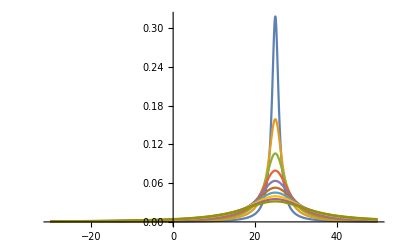

```mathematica
Plot[Evaluate@Table[PDF[CauchyDistribution[25,i],y],{i,1,10}],{y,-30,50},PlotRange->All]
```